# Inheritance properties in CA increasing definitions

The objective of this project is to demonstrate that there exists a behavioral inheritance that is naturally inherited from initial configurations. For this, the properties of the smallest definitions of cellular automata are analyzed and the relationship that these elements have in different spaces and configurations is explored. For this, the first step is to identify what the existing behaviors of a dimensionless automaton are, then how these rules propagate to one-dimensional spaces and finally, how the increase in states opens the possibility of universes of interconnected configurations with inherited properties.

As already mentioned, the first step to study inherited properties requires studying the properties of the initial configuration. Although Stephen Wolfram proposes ECA, this is certainly not the minimal configuration, since we can have a neighborhood of 2 elements and still have 16 rules. This configuration with a smaller number of rules has a smaller number of behaviors, so the properties exhibited here are not usually studied in depth, since there are no pseudo-random sequences and it is not Turing complete. But if we already defined a neighborhood of 2, is it possible to define a neighborhood of 1? Defining a neighborhood of a single element implies that it only depends on the value of one cell, but also implies that it can be a neighbor of itself, making it dimensionless. Well, the first part of this experiment consists of studying dimensionless cellular automata. More than the behavior, what interests us is analyzing the propagation of behaviors.

Usually the names of rules depend on the configuration, such as ECA or B3/S23 in life, but all rules can be defined as a decimal number. Since here we are going to study rules that belong to different spaces, it is necessary to distinguish the origin of each one of them. To start, we will use the following notation:

Where the rule represents the decimal number of the state vector and has as subscripts the number of states required by that rule along with the number of neighbors.

## Dimensionless Cellular Automaton

## One states

A CA that has a single state and a single neighbor can only have one possible transition rule, rule .

```mathematica
RulePlot[CellularAutomaton[{0,1,0}],ImageSize->100,PlotLegends->Placed[Subscript[0,2,1], Below]]
```

-Graphics-

This rule in that space is persistence: it does not change, it is reversible, periodic and constant. It is like an absolute zero. However, we cannot extract information or behaviors. For this it is necessary to expand the space of CAs, either by increasing the number of states or increasing the neighborhood and dimensionality; this first part focuses on increasing only the number of states.

For 2 states, we can generate the following  rules:

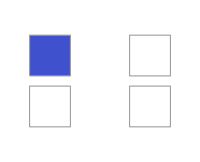
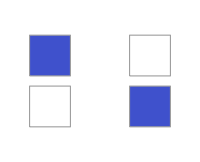
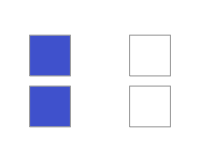
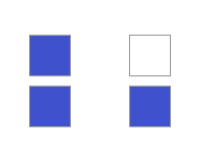
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{RulePlot[CellularAutomaton[{#,2,0}],ColorRules->colorRules,ImageSize->200,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@Range[0,3,1]}]
```

If we evolve all systems with those rules we can find a repeated behavior between rule  y . These convert everything to 0 and everything to 1 respectively, but if we make a permutation in the colors (states), we observe that we obtain the other rule. To associate all these rules, we use the function InverseRules, which receives the rule number, states and number of neighbors and returns all rules with the same behavior. 
Additionally, the function getAlluniqueRules can also be used, which only receives the number of states and neighbors and creates all the associations of that rule space. For example, these are the unique behaviors for 2 states and one neighbor:

```mathematica
getAllUniqueRules[2,1]
```

{0→{0,3},1→{1},2→{2}}

If we assume that the behavior of rule  is the same as that of rule , then we further reduce the number of different behaviors; however, rule  is not reversible, so it is not exactly the same, but it does have the same type of attractor. 
Rules  y  on the other hand are reversible and are the inverse rules of themselves.

These are the unique behaviors for 3 states. Again we find the pattern of rule , but in addition, we have new behaviors

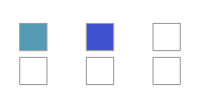
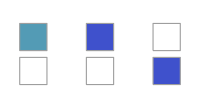
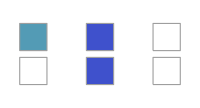
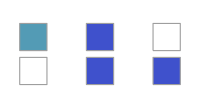
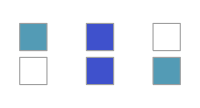
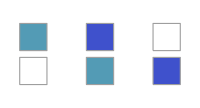
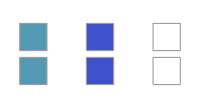
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
urs3=getAllUniqueRules[3,1];
Grid[Partition[RulePlot[CellularAutomaton[{#,3,0}],ColorRules->colorRules,ImageSize->200,PlotLegends->Placed[Subscript[#,3,1], Below]]&/@Keys[urs3],UpTo[4]]]
```

```mathematica
urs3={0,1,3,4,5,7,21};
Grid[Partition[RulePlot[CellularAutomaton[{#,3,0}],ColorRules->colorRules,ImageSize->100,PlotLegends->Placed[Subscript[#,3,1], Below]]&/@urs3,UpTo[4]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

: Same like the rule .

: This is a rule with a period-2 attractor that is not reversible. This rule shares some similarity with  by having a periodic attractor.

: This rule has 2 fixed-point attractors. This rule shares some similarity with .

: This rule has 1 fixed-point attractor. This rule shares some similarity with .

: This rule has 1 periodic attractor and 1 fixed-point attractor, and therefore shares similarity with rules  and .

: Rule  has the same behavior as , as it is an attractor whose period is defined by the number of states, and it is its own inverse rule.

: Rule  has the same behavior as , as it is a constant attractor with period 1 and is its own inverse.

Performing the manual analysis turns out to be exhaustive and impractical because even though we say it “shares similarity” by the way its attractor behaves, we do not have a metric or a consistent way to define such relationships; that is why, instead of exploring through an individual analysis, we seek to define a direct association between them.

To run the tests, the following iconized element is used, which stores all unique behaviors for the first 7 states. Although the neighborhood is 1, there are still  rules, so the calculation grows exponentially.

```mathematica
urs=;
```

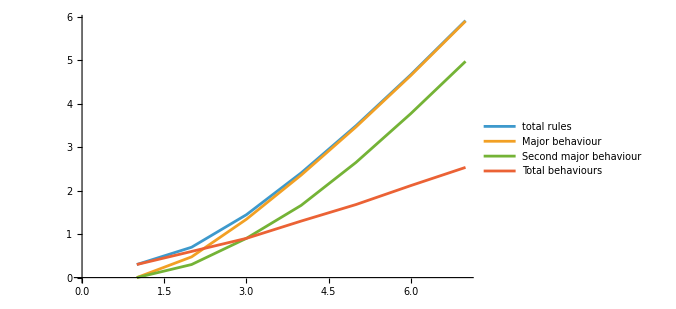

```mathematica
ListLinePlot[
Transpose[MapThread[{#1^#1,#2[[-1,1]],If[Length[#2]>=2,#2[[-2,1]],0],Length[#2]}&,{Range[7],urs}]],
ScalingFunctions->"SignedLog",
PlotLegends->{"total rules","Major behaviour","Second major behaviour","Total behaviours"},
ImageSize->500
]
```

Next, the rules grouped by number of states are shown. We can observe that all rules with  states are a subset of the rules with  states, with the difference that the new state is assigned a transition to 0 (the first state).

```mathematica
burs=Table[IntegerDigits[#,Max[2,i],i]&/@urs[[i,;;,1]],{i,1,Length[urs]}];
Module[{cell=10,maxRows=20},
Grid[{With[{nrows=Min[maxRows,Dimensions[#][[1]]],
ncols=Dimensions[#][[2]]},
ArrayPlot[#[[;;UpTo[maxRows]]],
ColorRules->colorRules,
Mesh->True,
PlotRangePadding->0,
ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},
ImageSize->{cell*ncols,cell*maxRows}]]&/@burs
},Spacings->{2, 0}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

The first hypothesis was that there existed a way to generate that entire sequence through an algorithm or formula, and then there was a function that extracted only the rules that belonged to that space. This could not be demonstrated since the generated sequence is random, or at least a universal pattern could not be found, but only isolated patterns. It is interesting how within the very definition of cellular automata we can find these complex forms.

The next hypothesis was that there exists a mapping between rules that allows us to move between CA spaces. That is, we can move from rule  a la  simply by adding a new state that points to state 0. But the question arises: do they all have the same behavior? Let us show the evolutions for some examples.

Rules {0,0,0,0,0,0,0}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],2]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,0}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,0,0,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,1}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,1,1,2}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,2}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,1,1,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,1}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics-

We observe that the behavior is practically the same, since the last state only makes a call to the first one. From this we infer 2 things. If rule  is reversible, rule  is not, where x y  have the same rule vector. 
Now, if we can apply the function of adding a new state with a transition to the empty element, it must also be possible to perform the inverse process, that is, a rule whose last state has a transition to 0 can be removed as long as no other state has a transition to the last state. This holds for the examples already shown; what we are doing is moving between the subsets of the rule space. But there are exceptional cases that do not seem to satisfy this, for example, rule , which if we remove the last transitions we obtain the following rules:

```mathematica
Grid[{Module[{cas={CellularAutomaton[{31,5,0},Range[4,0,-1],5],CellularAutomaton[{21,4,0},Range[3,0,-1],5],CellularAutomaton[{13,3,0},Range[2,0,-1],5]},labels={Subscript[31,5,1],Subscript[21,4,1],Subscript[13,3,1]},cell=30},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},MapThread[With[{nrows=Dimensions[#1][[1]],ncols=Dimensions[#1][[2]]},ArrayPlot[#1,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,PlotLabel->#2,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&,{cas,labels}]]]}]
```

-Graphics-

But rules ,  do not belong to the list of unique behaviors; however, we can apply the function InverseRules to find the representative of that behavior and discover where that pattern comes from. By doing this, we discover that rule  has the following pattern when applying the two possible functions. This process ends when neither of the 2 operations can be performed.

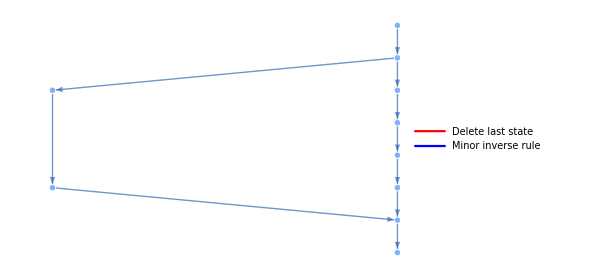

```mathematica
Module[{
vectors={{0,0,1,1,1},{0,1,1,1},{1,1,1},{0,0,0},{0,0},{0},{0,0,2,0},{0,2,0},{0,1,1},{1,1}},
edges={{0,0,1,1,1}->{0,1,1,1},{0,1,1,1}->{1,1,1},{1,1,1}->{0,0,0},{0,0,0}->{0,0},{0,0}->{0},{0,1,1,1}->{0,0,2,0},{0,0,2,0}->{0,2,0},{0,2,0}->{0,1,1},{0,1,1}->{1,1},{1,1}->{0,0}},
colores={({0,0,1,1,1}->{0,1,1,1})->Red,({1,1}->{0,0})->Blue,({0,1,1,1}->{1,1,1})->Red,({0,0,0}->{0,0})->Red,({0,0}->{0})->Red,({0,0,2,0}->{0,2,0})->Red,({0,1,1}->{1,1})->Red,({1,1,1}->{0,0,0})->Blue,({0,1,1,1}->{0,0,2,0})->Blue,({0,2,0}->{0,1,1})->Blue}},
Legended[LayeredGraph[
Graph[
edges,
EdgeStyle->colores,
VertexShapeFunction->(Inset[
ArrayPlot[{#2},
ColorRules->colorRules,
ImageSize->{Length[#2]*20,20},
Mesh->True,
MeshStyle->Gray,
ImagePadding->0,
PlotRangePadding->0
],#1]&),
VertexSize->{0.01,0.25}],
ImageSize->{450,Automatic}
],LineLegend[colores[[All,2]],{"Delete last state","Minor inverse rule"}]]
]
```

We can replicate this process for any rule, regardless of the number of states; next, some examples are shown for different numbers of states.

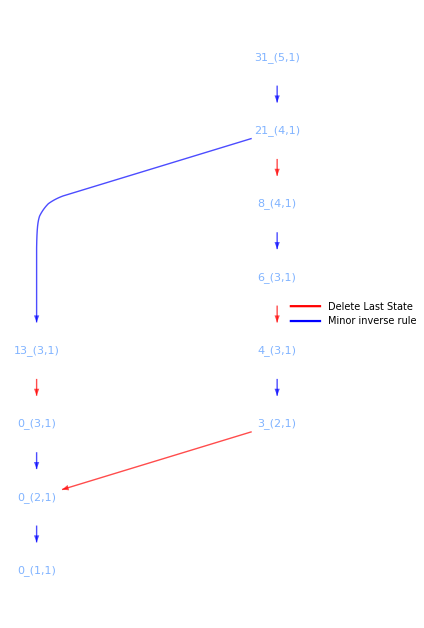
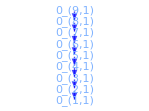
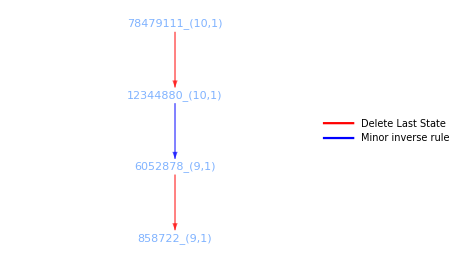
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{rulialGraph[getTransitions[{31,5,0}]],
rulialGraph[getTransitions[{0,9,0}]],
rulialGraph[getTransitions[{78479111,10,0}]]
}}]
```

Next, the hypergraph of all existing relationships is shown. Each node contains all the rules with the same behavior; they are the elements that share the mesh. The height represents the number of states and the downward arrows point to the rule whose behavior they imitate. As already demonstrated, there are rules that do not inherit from others, that is, whose behavior is unique. With this, in addition to significantly reducing the number of behaviors when adding more states, the behavioral relationships are also shown.

```mathematica
Import["./trans_0d.pdf"][[1]]
```

-Graphics-

## Functions

## Prebuilt functions

```mathematica
(*Hay que asociar las reglas*)
cas=Flatten[Table[
u=urs[[i]];
Subscript[#,i,0]&/@#&/@u[[;;,2]]
,{i,1,5}],1];
transitions=DeleteDuplicates[{Subscript@@#[[1]],Subscript@@#[[2]]}&/@Flatten[getTransitions[{#[[1]],#[[2]],#[[3]]}]&/@cas[[;;,1]]]];
```

```mathematica
cas=;
transitions=;
Hypergraph3D[cas,transitions,70,8,1.4]
```

-Graphics3D-

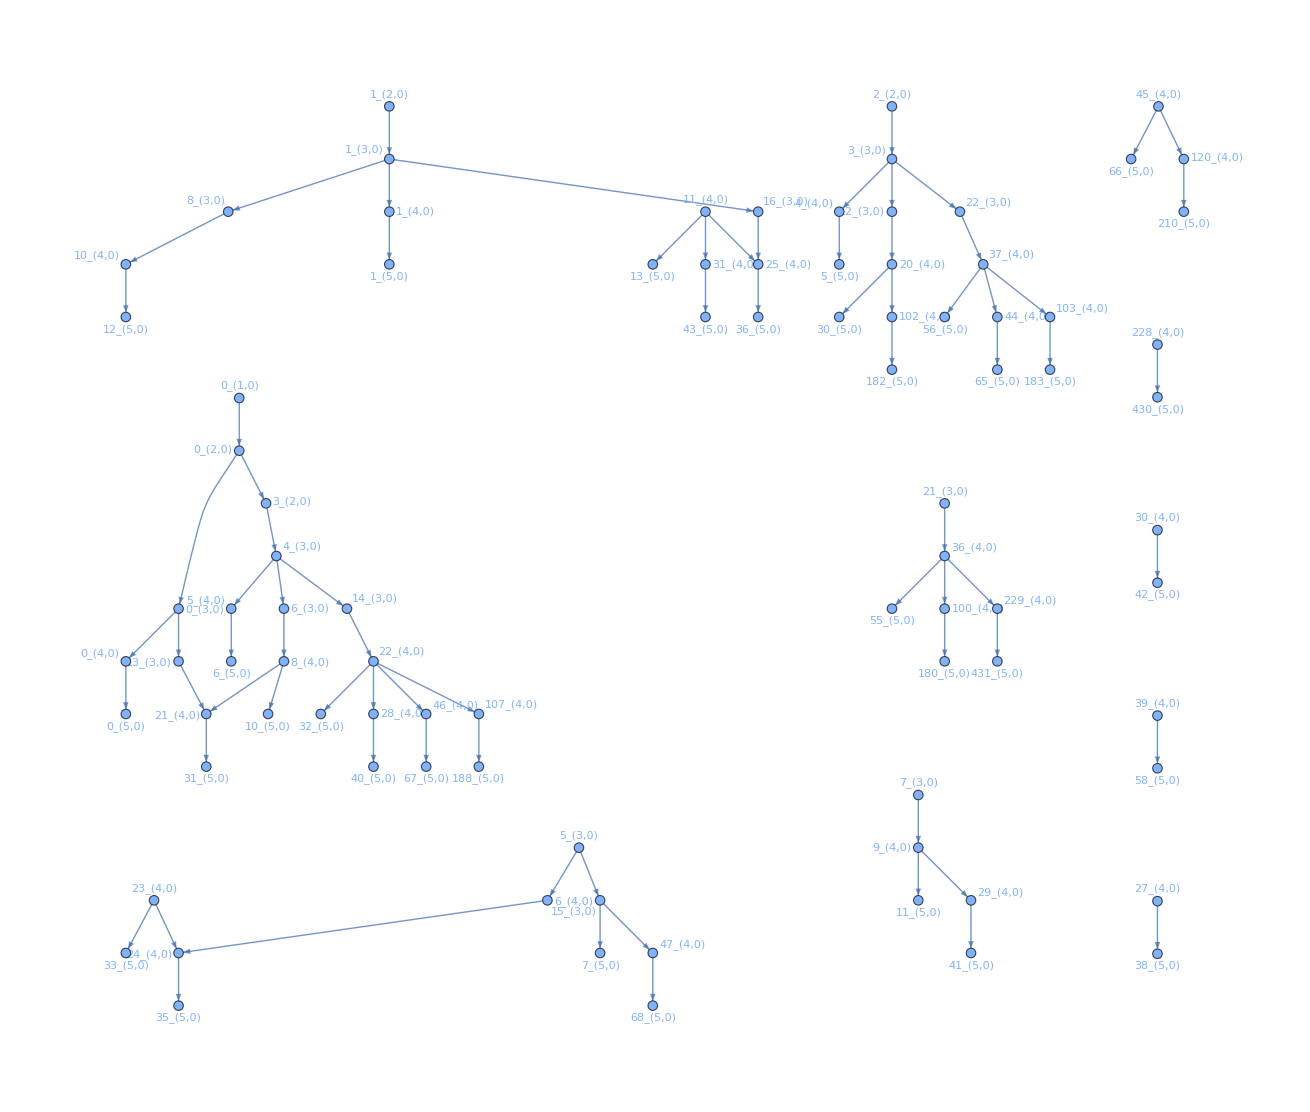

```mathematica
Graph[#[[2]]->#[[1]]&/@transitions,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

## Functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
InverseRules[ca_List]:=Module[
{
r=ca[[1]],s=ca[[2]],n=ca[[3]],
L=ca[[2]]^(2ca[[3]]+1),outputs,tuples,perms
},
outputs=Reverse[IntegerDigits[r,s,L]];(*outputs[[k]]=salida de la vecindad k-1*)
tuples=IntegerDigits[#,s,(2n+1)]&/@Range[0,L-1];(*tuples[[k]]=vecindad k-1 como n-tupla*)
perms=Permutations[Range[0,s-1]];(*solo s! permutaciones de ESTADOS*)
Sort@DeleteDuplicates@Table[
Module[
{pi=AssociationThread[Range[0,s-1]->perm],newOut=ConstantArray[0,L]},
Do[
newOut[[FromDigits[pi/@tuples[[k]],s]+1]]=pi[outputs[[k]]]
,{k,1,L}
];
FromDigits[Reverse[newOut],s]]
,{perm,perms}
]
]
```

```mathematica
minPermutation[ca_]:=Module[{in},
in=InverseRules[ca[[1]],ca[[2]],1][[1]];
If[in!=ca[[1]],
{in,ca[[2]],0}]
]
```

```mathematica
deleteState[ca_]:=Module[{a=IntegerDigits[ca[[1]],ca[[2]],ca[[2]]]},
If[a[[1]]==0&&Length[a]>Max[a]+1,
a=a[[2;;]];
{FromDigits[a,ca[[2]]-1],ca[[2]]-1,0}
]
];
```

```mathematica
getTransitions[ca_]:=Module[
{inverse={},delete={},unvisited={ca},visited={},c,ir,dr},

While[Length[unvisited]!=0,
c=unvisited[[1]];
unvisited=unvisited[[2;;]];
If[MemberQ[visited,c],Continue[];,
AppendTo[visited,c];
];

ir=minPermutation[c];
dr=deleteState[c];

If[Length[ir]==3,
AppendTo[inverse,c->ir];
AppendTo[unvisited,ir];
];
If[Length[dr]==3,
AppendTo[delete,c->dr];
AppendTo[unvisited,dr];
];
];

{inverse,delete}
]
```

```mathematica
getAllUniqueRules[s_Integer,n_Integer]:=Module[
{rules=Range[0,s^s^n - 1],
uniqueRules={},
rule},

While[Length[rules]!=0,
rule=rules[[1]]->InverseRules[rules[[1]],s,n];
AppendTo[uniqueRules,rule];
rules=DeleteElements[rules,rule[[2]]];
];
uniqueRules
]
```

```mathematica
countAtractors[ca_]:=Module[{
atractors={},
a,visited,atracted,atractorCount
},
Do[
a=CellularAutomaton[ca,{i},2ca[[2]]][[ca[[2]];;]];
visited={};
atracted={};
atractorCount=0;
Do[
If[ContainsAny[visited,{e}],
AppendTo[atracted,visited[[-1]]->e]
Break[];,
If[Length[visited]!=0,AppendTo[atracted,visited[[-1]]->e]];
AppendTo[visited,e];
atractorCount++;
];
,{e,a}];
AppendTo[atractors,atracted];
atractorCount
,{i,0,ca[[2]]-1}
];

Sort@Counts[Length/@DeleteDuplicates[Sort/@atractors]]
];
```

```mathematica
addTransitions[transitionsIn_List,casIn_List]:=Module[
{
transitions=transitionsIn,cas=casIn,
visited,unvisited,last={},ca,caI,head,validPreds,cae,caD
},
visited=EdgeList[transitions][[;;,2]];
unvisited=Complement[DeleteDuplicates[{InverseRules[#][[1]],#[[2]],#[[3]]}&/@cas],visited];

While[Length[unvisited]!=0,
ca=unvisited[[1]];
unvisited=Rest[unvisited];

(*Obtener la cabeza cononica*)
caI=InverseRules[ca];
head={caI[[1]],ca[[2]],ca[[3]]};
ca=head;
If[MemberQ[visited,head],
last={};
Continue[];
];

If[Length[last]!=0,
AppendTo[transitions,last->head];
last={};
];

(*filtrar predecesores válidos Y no visitados*)
validPreds=Select[caI,#<ca[[2]]^(ca[[2]]-1)&&Not@ContainsAny[IntegerDigits[#,ca[[2]],ca[[2]]],{ca[[2]]-1}]&];
cae={#,ca[[2]],ca[[3]]}&/@validPreds;

cae=Complement[cae,visited];
AppendTo[visited,head];

If[Length[cae]==0,
Continue[];
];
caD=deleteState[cae[[1]]];

If[Length[caD]==0,
Continue[];
];

last=head;
PrependTo[unvisited,caD];
];

transitions
]
```

## Unprotected functions

```mathematica
Unprotect[RulePlot];

RulePlot[CellularAutomaton[{0,1,0}],opts:OptionsPattern[]]:=Module[{imgSize=Lookup[{opts},ImageSize,100],legend=Lookup[{opts},PlotLegends,None],restOpts=FilterRules[DeleteCases[{opts},(ImageSize|PlotLegends|ColorRules)->_],Options[Graphics]]},With[{g=Graphics[{RulePlot[CellularAutomaton[{0,2,0}]][[1,1,1,2]],{GrayLevel[0.8],{Line[{{0.6153846153846154,0},{0.6153846153846154,1}}],Line[{{1.2307692307692308,0},{1.2307692307692308,1}}]},{Line[{{0.6153846153846154,0},{1.2307692307692308,0}}],Line[{{0.6153846153846154,1},{1.2307692307692308,1}}]}}},ImageSize->imgSize,Sequence@@restOpts]},If[legend===None,g,Legended[g,legend]]]];

Protect[RulePlot];
```

```mathematica
Unprotect[IntegerDigits];
IntegerDigits[0,1,1]:={0};
Protect[IntegerDigits];
```

## Plot functions

```mathematica
plantilla=;
blanco=ConstantArray[-1,7];
align[m_]:=Module[
{salida={},p=1},
Do[
If[p<=Length[m]&&m[[p]]===fila,
AppendTo[salida,fila];
p++,
AppendTo[salida,blanco]
]
,{fila,plantilla}
];
salida
];
```

```mathematica
colorRules=Join[{-1->Black,0->RGBColor[1., 1., 1.]},Table[k->ColorData["Rainbow"][k/5],{k,1,5}]];
```

```mathematica
rulialGraph[trans_,colorA_:Red,colorB_:Blue,labelA_:"Delete Last State",labelB_:"Minor inverse rule"]:=Module[
{
edges=Join[trans[[1]],trans[[2]]],
edgeStyles=Join[(#->Directive[colorA,Thick])&/@trans[[1]],(#->Directive[colorB,Thick])&/@trans[[2]]],
nodePlot=Function[v,If[v[[2]]<1,Graphics[{GrayLevel[0.9],Rectangle[]},ImageSize->{30,25}],RulePlot[CellularAutomaton[v],ImageSize->{Automatic,25},ColorRules->colorRules]]]
},
Legended[
LayeredGraph[
Graph[
edges,
EdgeStyle->edgeStyles,
VertexShapeFunction->(Inset[Column[{nodePlot[#2],Style[Subscript[#2[[1]],#2[[2]],1],Small,Black]},Alignment->Center],#1]&),
VertexSize->{0.11,100.03}
],
ImageSize->{Automatic,Automatic},
AspectRatio->2],
LineLegend[{colorA,colorB},{labelA,labelB}]
]
]
```

```mathematica
Hypergraph3D[meshes_List, transitions_List, hScale_: 40, rad_: 1.5, nSize_: 0.5] :=
  Module[{rThick = 0.04, maxSpread = 4.,
    mL = meshes, tL = transitions,
    nodeH, circEdgesForMesh, heightNodesEdges,
    allNodes, allCircEdges, meshesByHeight, nodePos, nodeToMeshIdx,
    sortedH, savedPos2D,
    rings, rings3D, tEdges3D, nodeSpheres3D, ringLabels3D, planes3D},

   (* Normalizar formato: reglas -> listas, nodos envueltos en lista -> nodos bare *)
   mL = mL /. Rule[a_, b_] :>
       Join[If[ListQ[a], a, {a}], If[ListQ[b], b, {b}]];
   tL = {If[ListQ[#[[1]]], First[#[[1]]], #[[1]]],
         If[ListQ[#[[2]]], First[#[[2]]], #[[2]]]} & /@ tL;

   nodeH[n_]           := If[ListQ[n], n[[1, 2]], n[[2]]];
   circEdgesForMesh[m_] := If[Length[m] < 2, {},
     Table[DirectedEdge[m[[j]], m[[Mod[j, Length[m]] + 1]]], {j, Length[m]}]];

   allNodes       = DeleteDuplicates[Flatten[mL]];
   allCircEdges   = Flatten[circEdgesForMesh /@ mL];
   meshesByHeight = GroupBy[mL, nodeH[#[[1]]] &];

   heightNodesEdges[hs_List] := Block[{hn, he, ht},
     hn = DeleteDuplicates[Flatten[Flatten[meshesByHeight /@ hs, 1]]];
     he = Flatten[circEdgesForMesh /@ Flatten[meshesByHeight /@ hs, 1]];
     ht = DirectedEdge[#[[1]], #[[2]]] & /@
       Select[tL, MemberQ[hn, #[[1]]] && MemberQ[hn, #[[2]]] &];
     {hn, DeleteDuplicates[Join[he, ht]]}];

   (* Eliminar transiciones intra-malla *)
   nodeToMeshIdx = Association @ Flatten[
     MapIndexed[Function[{mesh, idx}, # -> First[idx] & /@ mesh], mL]];
   tL = Select[tL,
     Lookup[nodeToMeshIdx, #[[1]], -1] =!= Lookup[nodeToMeshIdx, #[[2]], -2] &];

   (* FASE 1: posiciones 2D en cascada top-down *)
   sortedH    = Reverse[Sort[Keys[meshesByHeight]]];
   savedPos2D = <||>;

   Block[{cn, ce, g, pa},
     {cn, ce} = heightNodesEdges[Take[sortedH, Min[2, Length[sortedH]]]];
     g  = Graph[cn, ce];
     pa = AssociationThread[VertexList[g], GraphEmbedding[g]];
     Do[savedPos2D[v] = pa[v], {v, cn}]];

   Do[Block[{upperH, lowerH, uNodes, lNodes, cn, ce, init, g, pa},
     upperH = sortedH[[i]]; lowerH = sortedH[[i + 1]];
     uNodes = DeleteDuplicates[Flatten[meshesByHeight[upperH]]];
     lNodes = DeleteDuplicates[Flatten[meshesByHeight[lowerH]]];
     {cn, ce} = heightNodesEdges[{upperH, lowerH}];
     init = Join[Thread[uNodes -> (savedPos2D /@ uNodes)],
                 Thread[lNodes -> Table[{0., 0.}, {Length[lNodes]}]]];
     g  = Graph[cn, ce, VertexCoordinates -> init];
     pa = AssociationThread[VertexList[g],
            GraphEmbedding[g, "SpringElectricalEmbedding"]];
     Do[pa[v] = savedPos2D[v], {v, uNodes}];
     Do[savedPos2D[v] = pa[v], {v, lNodes}]
   ], {i, 2, Length[sortedH] - 1}];

   (* FASE 2: coordenadas 3D con escalado por centroide por altura *)
   rings = {};
   Block[{rawCX, hRangesX, hRangesZ, largestH, targetRX, targetRZ},
     rawCX = Association @ Table[h -> Table[
       Block[{m = meshesByHeight[h][[k]], pts},
         pts = savedPos2D /@ m;
         {Mean[pts[[All, 1]]], Mean[pts[[All, 2]]]}],
       {k, Length[meshesByHeight[h]]}],
     {h, Keys[meshesByHeight]}];

     hRangesX = Association @ Table[h -> Block[{cx = rawCX[h]},
       If[Length[cx] < 2, 0.001, Max[cx[[All, 1]]] - Min[cx[[All, 1]]]]],
     {h, Keys[meshesByHeight]}];
     hRangesZ = Association @ Table[h -> Block[{cx = rawCX[h]},
       If[Length[cx] < 2, 0.001, Max[cx[[All, 2]]] - Min[cx[[All, 2]]]]],
     {h, Keys[meshesByHeight]}];

     largestH = MaximalBy[Keys[meshesByHeight], hRangesX[#] + hRangesZ[#] &][[1]];
     targetRX = Max[hRangesX[largestH], 0.001];
     targetRZ = Max[hRangesZ[largestH], 0.001];

     Do[Block[{hMeshes = meshesByHeight[h], cx = rawCX[h], xMid, zMid, sfX, sfZ},
       xMid = Mean[{Min[cx[[All, 1]]], Max[cx[[All, 1]]]}];
       zMid = Mean[{Min[cx[[All, 2]]], Max[cx[[All, 2]]]}];
       sfX  = targetRX / Max[hRangesX[h], 0.001];
       sfZ  = targetRZ / Max[hRangesZ[h], 0.001];
       Do[Block[{m = hMeshes[[k]], n, scx, scz},
         n   = Length[m];
         scx = (cx[[k, 1]] - xMid) * sfX;
         scz = (cx[[k, 2]] - zMid) * sfZ;
         If[n == 1,
           nodePos[m[[1]]] = {scx, h*hScale, scz},
           Do[nodePos[m[[j]]] = {scx + rad*Cos[2 Pi (j-1)/n],
                                  h*hScale,
                                  scz + rad*Sin[2 Pi (j-1)/n]}, {j, n}]];
         AppendTo[rings, {{scx, h*hScale, scz}, m[[1]]}]
       ], {k, Length[hMeshes]}]
     ], {h, Keys[meshesByHeight]}]
   ];

   (* Planos translúcidos por altura *)
   planes3D = Flatten[Function[h, Block[{hPos, x1, x2, z1, z2},
     hPos = Select[nodePos /@ DeleteDuplicates[Flatten[meshesByHeight[h]]],
                   VectorQ[#, NumericQ] &];
     If[Length[hPos] == 0, {},
       x1 = Min[hPos[[All, 1]]] - rad*1.5; x2 = Max[hPos[[All, 1]]] + rad*1.5;
       z1 = Min[hPos[[All, 3]]] - rad*1.5; z2 = Max[hPos[[All, 3]]] + rad*1.5;
       {Opacity[0.07], RGBColor[0.4, 0.6, 1.], EdgeForm[None],
        Polygon[{{x1, h*hScale, z1}, {x2, h*hScale, z1},
                 {x2, h*hScale, z2}, {x1, h*hScale, z2}}]}]
   ]] /@ Keys[meshesByHeight], 1];

   (* FASE 3: primitivas 3D *)
   rings3D = {GrayLevel[0.5], Opacity[0.25], Specularity[White, 10],
     Function[r, Tube[Table[{r[[1, 1]] + rad*Cos[t], r[[1, 2]],
          r[[1, 3]] + rad*Sin[t]}, {t, 0, 2 Pi, Pi/30}], rThick]] /@ rings};
   tEdges3D = {RGBColor[1, 0.596, 0], AbsoluteThickness[2], Arrowheads[0.02],
     Arrow[{nodePos[#[[1]]], nodePos[#[[2]]]}] & /@ tL};
   nodeSpheres3D = Flatten[Function[v, With[{p = nodePos[v]},
     {RGBColor[0, 0.141, 0.927], Sphere[p, nSize]}]] /@ allNodes, 1];
   ringLabels3D = Text[
      Framed[#[[2]],
        Background -> RGBColor[1, 1, 1, 0.8],
        FrameMargins -> 0,
        FrameStyle -> Dotted],
      #[[1]] + {0, nSize*2.5, 0}
    ] & /@ rings;

   Graphics3D[
    {planes3D, rings3D, tEdges3D, nodeSpheres3D, ringLabels3D},
    Boxed      -> True,
    BoxStyle   -> Directive[GrayLevel[0.65], Thin, Opacity[0.4]],
    Axes       -> {False, True, False},
    AxesLabel  -> {None, Style["States", Black, Bold, 14], None},
    AxesStyle  -> Directive[Black, 12],
    Ticks      -> {None, Table[{h*hScale, h}, {h, Keys[meshesByHeight]}], None},
    Lighting   -> "Neutral",
    ImageSize  -> {700, 700}]]
```

```mathematica
CaRulePlot[ca_List]:=
RulePlot[CellularAutomaton[ca],ColorRules->colorRules];
```